# 雅可比矩阵的几何意义

```mathematica
StreamDensityPlot[{x^2,y^2},{x,-3,3},{y,-3,3}]
```

-Graphics-

```mathematica
J={{2x,0},{0,2y}};
StreamDensityPlot[J.{x^2,y^2},{x,-3,3},{y,-3,3}]
```

-Graphics-

### 雅可比矩阵

```mathematica
DynamicModule[{r,pts,pts2,pts3,px,py,o,f},r=10;pts=Table[{x,y},{x,-r,r},{y,-r,r}];
pts2=Map[f,pts,{2}];{px,py}={2,2};f[{x_,y_}]:={x+Sin[y],y+Sin[x]};
LocatorPane[Dynamic[{px,py}],
Dynamic[pts3=Table[{{1,Cos[py]},{Cos[px],1}}.{x,y},{x,px-1,px+1,0.4},{y,py-1,py+1,0.4}];Graphics[{{Thin,Line[pts3],Line[pts3ᵀ]},Magenta,Line[pts2],Line[pts2ᵀ],Magenta,PointSize[Large],Point[f[{px,py}]]},PlotRange->r,GridLines->Automatic,GridLinesStyle->Directive[Orange,Dashed],Axes->True,ImageSize->Large]]]]
```

```mathematica
Slider[Dynamic[px],{-1,10}]
Dynamic[py=px;{{2px,-1},{0,3 py^2}}.{px,py}/5-{px^2-py,py^3}/5]
```

```mathematica
Slider[Dynamic[px],{-1,10}]
Dynamic[py=px;Det[{{2px,-1},{0,3 py^2}}/5]]
```

### 方式一

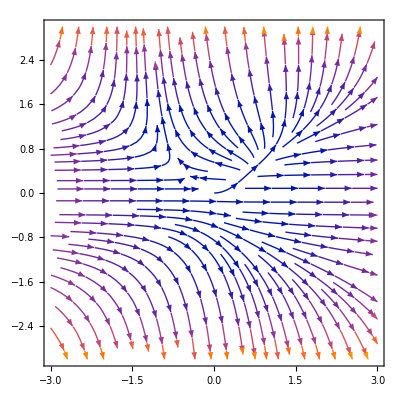

```mathematica
StreamPlot[{x^2-y,y^3},{x,-3,3},{y,-3,3}]
```

```mathematica
{x1,y1}={1,0};
Slider2D[Dynamic[{x1,y1}],{-3,3}]
Dynamic@StreamPlot[{{x^2-y,y^3},{{2x1,-1},{0,3 y1^2}}.{x,y}},{x,-3,3},{y,-3,3}]
```

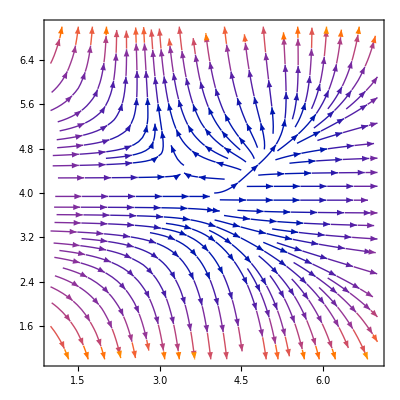

```mathematica
ListStreamPlot[Table[{x^2-y,y^3},{x,-3,3},{y,-3,3}]]
```